## General definitions

Set to current directory.

```mathematica
SetDirectory@NotebookDirectory[];
```

Filenames -- same as in “cDMRG_input.”

```mathematica
namestr[x_?StringQ,y_?NumericQ]:="_"<>x<>If[0<y<0.001||y>=10^4,"_1E"<>ToString@Rationalize[Log[10,y],0],"_"<>ToString[y]];
namestr[x_?StringQ,y_?StringQ]:="_"<>x<>"_"<>y;
namestr[list_?MatrixQ]:=StringDrop[StringJoin[namestr@@@list],1];
```

```mathematica
name:=namestr[{{"N",particles},{"gamma",gamma},{"Nwells",numwells},{"V0",V0byEr},{"M",numsegments},{"basisparams",basisid},{"sweepparams",epsid}}]<>"_ITensor"
```

```mathematica
inputname:="Runs/"<>name<>".txt";
outputname:="Runs/"<>name<>".out";
errorname:="Runs/"<>name<>".error";
ehistname:="Runs/"<>name<>"_ehist.m";
finalmeasname:="Runs/"<>name<>"_finalmeas.m";
spcorrname:="Runs/"<>name<>"_spcorrcoef.m";
nnavgname:="Runs/"<>name<>"_nnavgcoef.m";
entropyname:="Runs/"<>name<>"_entropy.m";
psiname:="Runs/"<>name<>"_psi_MMAformat.dat";
```

Make a Hermitian matrix/array from the upper half.

```mathematica
makeHermitian[upper_/;VectorQ[upper,VectorQ]]:=
MapThread[Join,{Conjugate@Reverse@Flatten[Reverse[upper,2],{{2},{1}}],Rest/@upper}];
makeHermitian[upper_/;VectorQ[upper,VectorQ[#,MatrixQ]&]]:=
MapThread[Join,{Map[ConjugateTranspose,Reverse@Flatten[Reverse[upper,2],{{2},{1}}],{2}],Rest/@upper}]
```

## Sample result

## Parameters

```mathematica
particles=4;
gamma=10;
numwells=4;
V0byEr=1;
numsegments=8;
basisid=1;
epsid=1;
saveid=1;
```

## Final measurements

```mathematica
finalmeas=Import[finalmeasname];
Short[finalmeas,2]
```

{sweepnums→{2,2,3,3,6,2},energies→{195.69590805963702,«39»,«38»,«38»,«38»,251.178052888482199},«5»,CPU time→«38»,avgoccupations→{{0.524449},«4»}}

Number of actual sweeps and final bond dimensions for each DMRG cycle.

```mathematica
{sweepnums,bonddims}={"sweepnums","bonddims"}/.finalmeas
```

{{2,2,3,3,6,2},{20,30,40,50,37,34}}

CPU- and wall times for each cycle.

```mathematica
({"sweeptimesCPU","sweeptimesWall"}/.finalmeas)//N
```

{{4.88261,12.7588,22.164,21.9502,28.532,4.53811},{5.08217,13.4921,23.776,22.9833,30.1494,4.75821}}

Average occupation of all basis states.

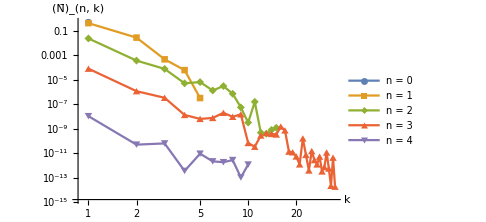

```mathematica
ListLogLogPlot[("avgoccupations"/.finalmeas),PlotRange->All,Joined->True,TicksStyle->Directive[Black,13],AxesLabel->(Style[#,Black,15]&/@{"k","(N̄)_(n, k)"}),PlotMarkers->Automatic,ImageSize->360,AxesStyle->AbsoluteThickness[1],PlotLegends->(Style["n = "<>ToString[#],Black,15]&/@Range[0,10])]
```

## Energy variation

Energy and discontinuity after each DMRG step.

```mathematica
ehist=Import[ehistname];
Short[Rest@ehist,4]
```

{{Ewpenalty→667.160973219776679,disc→49.585067915868287,E→171.310294061097608,center→1,dir→1,cputime→0.002907,walltime→0.005806,bonddim→2,eps→0.1},«250»,{Ewpenalty→251.178532260905485,disc→4.79373×10^-10,E→251.178052888482199,«3»,walltime→2.2751,bonddim→12,eps→1.×10^-6}}

We rescale by N E_r, where E_r is the recoil energy.

```mathematica
Er=(numwells*π)^2./2;
{Econt,Edisc}=Transpose[{"E","disc"}/.ehist]/{particles*Er,Er};
```

Energy E_c and discontinuity E_disc, as defined in the paper.

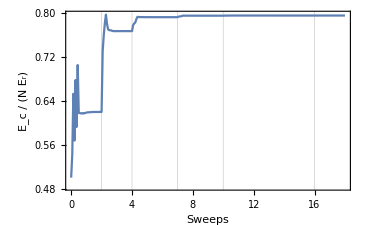
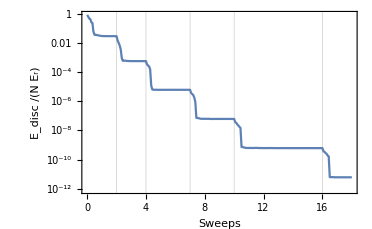

```mathematica
Row[{ListPlot[Econt,DataRange->{0,Total[sweepnums]},PlotRange->All,Joined->True,Frame->True,FrameTicksStyle->Directive[Black,13],FrameLabel->(Style[#,Black,15]&/@{"Sweeps","E_c / (N E_r)"}),GridLines->{Most@Accumulate[sweepnums],{}},ImageSize->365,FrameStyle->AbsoluteThickness[1]],
ListLogPlot[Edisc,DataRange->{0,Total[sweepnums]},PlotRange->All,Joined->True,Frame->True,FrameTicksStyle->Directive[Black,13],FrameLabel->(Style[#,Black,15]&/@{"Sweeps","E_disc /(N E_r)"}),GridLines->{Most@Accumulate[sweepnums],{}},ImageSize->372,FrameStyle->AbsoluteThickness[1]]},Spacer[20]]
```

Asymptotic value: As described in the paper, the energy  E_c at the end of each cycle approaches an asymptotic value  E_* as  E_*=E-η/Λ, where η is a constant and Λ is the penalty for discontinuities.  Thus, we can calculate  E_* from the final energies in the last two cycles.

```mathematica
finalens=("energies"/.finalmeas)/(particles*Er); (*final energies in each cycle*)
epsvals="eps"/.Import["Parameters/epstable.m"][[epsid,2]]; (*1/(Λ L) in each cycle*)
Estar=(epsvals[[-2]]*finalens[[-1]]-epsvals[[-1]]*finalens[[-2]])/(epsvals[[-2]]-epsvals[[-1]]) (*asymptotic value*)
```

0.795305

Check that E_c approaches E_* as 1/Λ.

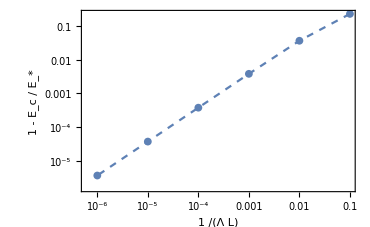

```mathematica
ListLogLogPlot[Transpose[{epsvals,1-finalens/Estar}],Joined->True,PlotRange->All,PlotMarkers->{Automatic,8},Frame->True,FrameTicksStyle->Directive[Black,13],FrameLabel->(Style[#,Black,15]&/@{"1 /(Λ L)","1 - E_c / E_*"}),ImageSize->370,FrameStyle->AbsoluteThickness[1],PlotStyle->Dashed]
```

## Single-particle correlations

As detailed in the supplement, two-point correlations of the form C(x,y) are given by piecewise polynomials. When x is in the i-th segment and y is in the j-th segment, define rescaled variables x̃:=(x-X_(i-1))/w_i and  ỹ:=(y-X_(j-1))/w_j, which vary between 0 and 1.  Then C(x,y)=C_(p,q)^(i,j)(x̃)^p(ỹ)^q.  The DMRG routine saves the coefficients  C_(p,q)^(i,j) for j>=i.

Import the polynomial coefficients.

```mathematica
spcorrcoefs=Import[spcorrname];
```

```mathematica
Length/@spcorrcoefs
```

{8,7,6,5,4,3,2,1}

Here is  C_(p,q)^(1,1).

```mathematica
spcorrcoefs[[1,1]]
```

SparseArray[…]

Evaluate the correlations on an arbitrarily fine grid.

```mathematica
divpts=N@Rest@Subdivide[20]; (*divide each segment into 20 points -- these are values of x̃,ỹ*)
exponents=Range[0,Length@spcorrcoefs[[1,1]]-1]; (*values of p,q*)
montable=divpts^#&/@exponents; (*all possible weights (x̃)^p*)
spcorrupper=Map[Transpose[montable].#.montable&,spcorrcoefs,{2}]; (*evaluate correlations for all j>=i*)
spcorrmat=ArrayPad[ArrayFlatten@makeHermitian@spcorrupper,{{1,0},{1,0}}]; (*Form a Hermitian matrix*)
```

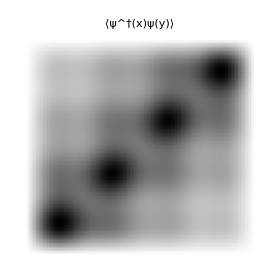

```mathematica
ArrayPlot[Reverse@spcorrmat,ImageSize->280,FrameLabel->{Style["x",Black,16],Style["y",Black,16]},FrameStyle->AbsoluteThickness[0.6],PlotLabel->Style["⟨ψ^†(x)ψ(y)⟩",Black,15]]
```

The density is simply given by the diagonal elements.

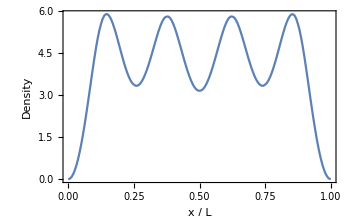

```mathematica
ListPlot[Diagonal[spcorrmat],Joined->True,DataRange->{0,1},PlotRange->All,Frame->True,FrameTicksStyle->Directive[Black,13],FrameLabel->(Style[#,Black,15]&/@{"x / L","Density"}),GridLines->{Subdivide[numsegments],{}},ImageSize->350,FrameStyle->AbsoluteThickness[1]]
```

## Entanglement entropy

The DMRG routine automatically saves the von Neumann entropy at the segment boundaries.

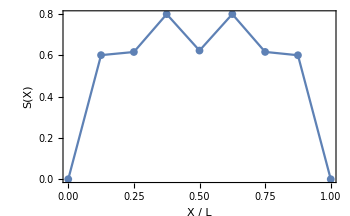

```mathematica
ListPlot[ArrayPad[Import[entropyname],1],Joined->True,DataRange->{0,1},PlotRange->All,PlotMarkers->{Automatic,8},Frame->True,FrameTicksStyle->Directive[Black,13],FrameLabel->(Style[#,Black,15]&/@{"X / L","S(X)"}),GridLines->{Subdivide[numsegments],{}},ImageSize->350,FrameStyle->AbsoluteThickness[1]]
```

To calculate the entropy at an arbitrary point, see the notebook “cDMRG_basis_splitting.”